#### import the data

```mathematica
importdata=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data.csv"];
data1=Values[Normal[importdata]]⟦All,2;;78⟧;
labels=Import["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data.csv"][[1]];
```

```mathematica
TeXForm[Table[{i,labels⟦i⟧},{i,1,78}]//TableForm]
```

\begin{array}{cc}
 1 & \text{PATIENT$\_$ID} \\
 2 & \text{age} \\
 3 & \text{age group} \\
 4 & \text{gender} \\
 5 & \text{Red blood cell count} \\
 6 & \text{White blood cell count} \\
 7 & \text{Hematocrit} \\
 8 & \text{globulin} \\
 9 & \text{Mean hemoglobin concentration} \\
 10 & \text{Monocytes ($\#$)} \\
 11 & \text{Lactate dehydrogenase} \\
 12 & \text{Urea} \\
 13 & \text{Lymphocyte ($\#$)} \\
 14 & \text{Gamma-glutamyl transpeptidase} \\
 15 & \text{Eosinophil ($\#$)} \\
 16 & \text{Creatinine} \\
 17 & \text{Neutrophils ($\#$)} \\
 18 & \text{Direct bilirubin} \\
 19 & \text{Bicarbonate} \\
 20 & \text{Uric acid} \\
 21 & \text{Aspartate aminotransferase} \\
 22 & \text{Average RBC volume} \\
 23 & \text{Total cholesterol} \\
 24 & \text{Lymphocytes ($\%$)} \\
 25 & \text{Platelet count} \\
 26 & \text{Eosinophils ($\%$)} \\
 27 & \text{albumin} \\
 28 & \text{Basophil ($\%$)} \\
 29 & \text{eGFR (based on CKD-EPI equation)} \\
 30 & \text{Total bilirubin} \\
 31 & \text{Alkaline phosphatase} \\
 32 & \text{Alanine aminotransferase} \\
 33 & \text{Hemoglobin} \\
 34 & \text{Mean hemoglobin content} \\
 35 & \text{Basophil ($\#$)} \\
 36 & \text{Neutrophils ($\%$)} \\
 37 & \text{Total protein} \\
 38 & \text{Monocytes ($\%$)} \\
 39 & \text{Indirect bilirubin} \\
 40 & \text{chlorine} \\
 41 & \text{calcium} \\
 42 & \text{Potassium} \\
 43 & \text{sodium} \\
 44 & \text{Hypersensitive C-reactive protein} \\
 45 & \text{Corrected calcium} \\
 46 & \text{International standardized ratio} \\
 47 & \text{Prothrombin time} \\
 48 & \text{Prothrombin activity} \\
 49 & \text{glucose} \\
 50 & \text{RBC distribution width SD} \\
 51 & \text{RBC distribution width CV} \\
 52 & \text{Average PLT volume} \\
 53 & \text{Platelet compression} \\
 54 & \text{Platelet ratio} \\
 55 & \text{PLT distribution width} \\
 56 & \text{D-D dimer quantification} \\
 57 & \text{Procalcitonin} \\
 58 & \text{Thrombin time} \\
 59 & \text{Activated partial thromboplastin time} \\
 60 & \text{Fibrinogen} \\
 61 & \text{Erythrocyte sedimentation rate} \\
 62 & \text{High-sensitivity cardiac troponin I} \\
 63 & \text{Quantification of hepatitis C antibody} \\
 64 & \text{Treponema pallidum antibody quantification} \\
 65 & \text{Quantification of hepatitis B surface antigen} \\
 66 & \text{HIV antibody quantification} \\
 67 & \text{Amino-terminal brain natriuretic peptide precursor (NT-proBNP)} \\
 68 & \text{PH} \\
 69 & \text{Interleukin 6} \\
 70 & \text{Tumor necrosis factor alpha} \\
 71 & \text{Interleukin 8} \\
 72 & \text{Interleukin 1-Beta} \\
 73 & \text{Interleukin 2 receptor} \\
 74 & \text{Interleukin 10} \\
 75 & \text{Ferritin} \\
 76 & \text{Antithrombin} \\
 77 & \text{Fibrin (pro) degradation products} \\
 78 & \text{Outcome} \\
\end{array}

## Classification

```mathematica
Prepend[Range[74]+2,2]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76}

### Survival probability by age and gender

randomize data for training/test split

```mathematica
SeedRandom[123];
rs=RandomSample[data1⟦All,{1,2,76}⟧,176];
```

Split data into 70% training and 30% test

```mathematica
trainingset=rs⟦1;;123⟧;
testset=rs⟦124;;176⟧;
```

```mathematica
c=Classify[data1⟦All,{1,3,77}⟧->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

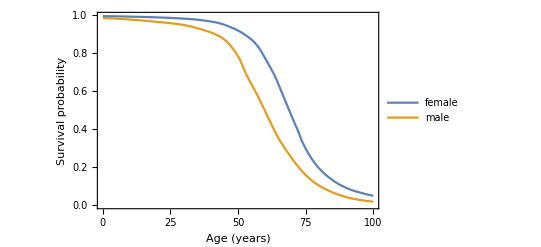

```mathematica
p[age_,gender_]:=c[{age,gender},{"Probability","survived"}];
Plot[{p[x,"female"],p[x,"male"]}, {x,0,100},PlotLegends->{"female","male"}, Frame->True,FrameLabel-> {"Age (years)", "Survival probability"}, Exclusions->None]
```

#### Accuracy and Confusion Matrix

```mathematica
cm=ClassifierMeasurements[c,testset->3]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.792453

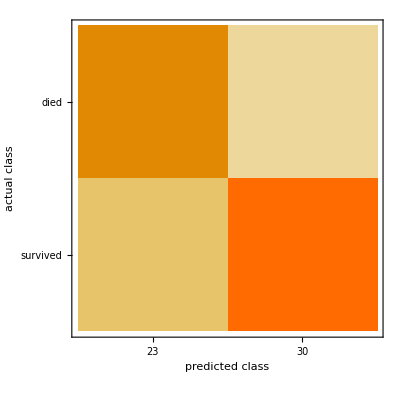

```mathematica
cm["ConfusionMatrixPlot"]
```

## Neural Network approach

#### training/test split of data

randomize data for training/test split

```mathematica
SeedRandom[123];
genrs=Table[RandomSample[data1⟦All,{i,3,77}⟧,176],{i,4,76,1}];
```

Split data into 75% training and 25% test

```mathematica
trainingset1=Table[genrs⟦i⟧⟦1;;132⟧,{i,1,73}];
testset1=Table[genrs⟦i⟧⟦133;;176⟧,{i,1,73}];
```

### classification by gender

```mathematica
ProgressIndicator[Dynamic[i],{4,76}]
```

```mathematica
c1=Table[Classify[trainingset1⟦i⟧->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"],{i,1,73}];
```

```mathematica
ProgressIndicator[Dynamic[k],{1,73}]
```

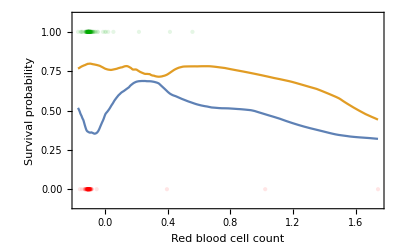
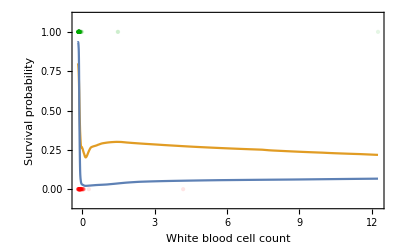
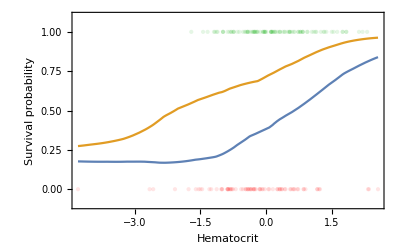
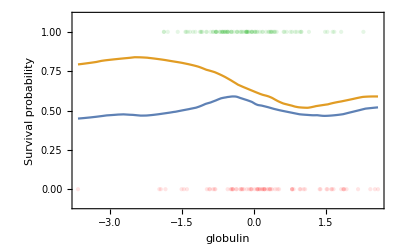
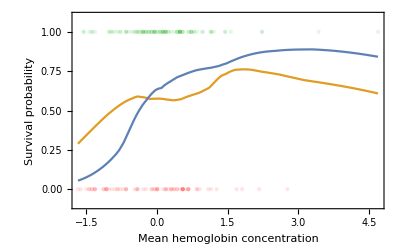
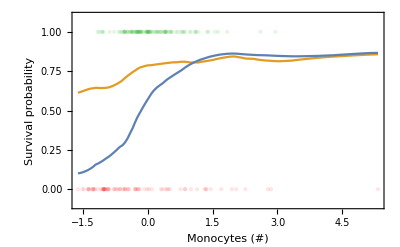
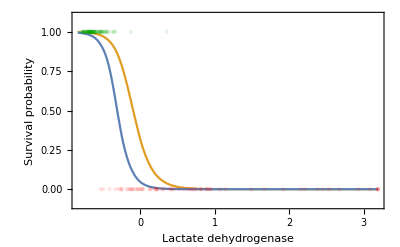
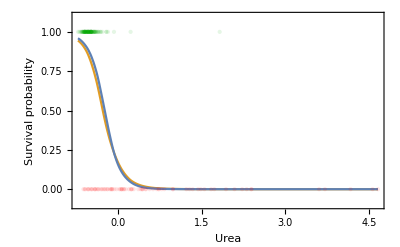
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Multicolumn[Table[Show[Plot[{c1⟦k⟧[{x,"female"},{"Probability","survived"}],c1⟦k⟧[{x,"male"},{"Probability","survived"}]}, {x,Min[trainingset1⟦k⟧⟦All,1⟧],Max[trainingset1⟦k⟧⟦All,1⟧]}, Frame->True,FrameLabel-> {labels⟦4+k⟧, "Survival probability"}, Exclusions->None,PlotRange->{-0.1,1.1},PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798]},Ticks->{Automatic,Range[0,1,0.2]}],ListPlot[{ArrayReshape[Riffle[data1⟦1;;99,3+k⟧,ConstantArray[1,Length[data1⟦1;;99,3+k⟧]]],{Length[data1⟦1;;99,3+k⟧],2}],ArrayReshape[Riffle[data1⟦100;;176,3+k⟧,ConstantArray[0,Length[data1⟦100;;176,3+k⟧]]],{Length[data1⟦100;;176,3+k⟧],2}]},PlotStyle->{Directive[Darker[Green],PointSize[Large],Opacity[0.1]],Directive[Red,PointSize[Large],Opacity[0.1]]}]],{k,1,73,1}],4,Appearance->"Horizontal"]
SwatchLegend[{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]},{"female","male","survived","died"},LegendFunction->"Frame"]
```

#### Confusion matrix and accuracy

```mathematica
cm1=Table[ClassifierMeasurements[c1⟦i⟧,testset1⟦i⟧->3],{i,1,73}];
```

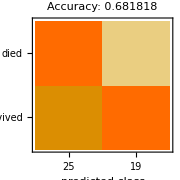
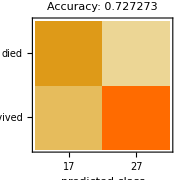
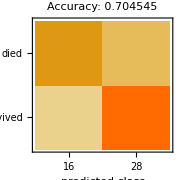
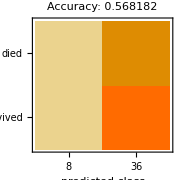
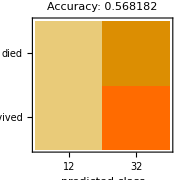
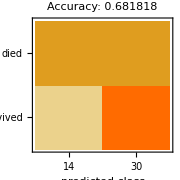
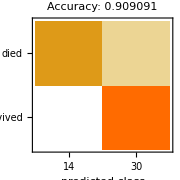
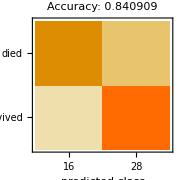
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  |  |  |

```mathematica
Multicolumn[Table[Show[cm1⟦i⟧["ConfusionMatrixPlot"],ImageSize->Small,PlotLabel->StringJoin["Accuracy: " ,ToString[cm1⟦i⟧["Accuracy"]]]],{i,1,73}],7,Appearance->"Horizontal"]
```

### classification by age group

#### training/test split of data

randomize data for training/test split

```mathematica
SeedRandom[123];
agers=Table[RandomSample[data1⟦All,{i,2,77}⟧,176],{i,4,76,1}];
```

Split data into 75% training and 25% test

```mathematica
trainingset2=Table[agers⟦i⟧⟦1;;132⟧,{i,1,73}];
testset2=Table[agers⟦i⟧⟦133;;176⟧,{i,1,73}];
```

```mathematica
ProgressIndicator[Dynamic[i],{4,76}]
```

```mathematica
ProgressIndicator[Dynamic[k],{1,73}]
```

```mathematica
c2=Table[Classify[trainingset2⟦i⟧->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"],{i,1,73}];
```

```mathematica
Multicolumn[Table[Show[{Plot[{c2⟦k⟧[{x,"young"},{"Probability","survived"}],c2⟦k⟧[{x,"middle age"},{"Probability","survived"}],c2⟦k⟧[{x,"old"},{"Probability","survived"}]}, {x,Min[trainingset2⟦k⟧⟦All,1⟧],Max[trainingset2⟦k⟧⟦All,1⟧]}, Frame->True,FrameLabel-> {labels⟦4+k⟧, "Survival probability"}, Exclusions->None,PlotRange->{-0.1,1.1},PlotStyle->{RGBColor[1, 0.75, 0],RGBColor[0.0575287, 0.697632, 0.634101],RGBColor[0.450866, 0.379481, 1.]}],ListPlot[{ArrayReshape[Riffle[data1⟦1;;99,3+k⟧,ConstantArray[1,Length[data1⟦1;;99,3+k⟧]]],{Length[data1⟦1;;99,3+k⟧],2}],ArrayReshape[Riffle[data1⟦100;;176,3+k⟧,ConstantArray[0,Length[data1⟦100;;176,3+k⟧]]],{Length[data1⟦100;;176,3+k⟧],2}]},PlotStyle->{Directive[Darker[Green],PointSize[Large],Opacity[0.1]],Directive[Red,PointSize[Large],Opacity[0.1]]}]}],{k,1,73,1}],4,Appearance->"Horizontal"]
SwatchLegend[{RGBColor[1, 0.75, 0],RGBColor[0.0575287, 0.697632, 0.634101],RGBColor[0.450866, 0.379481, 1.],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]},{"young","middle age","old","survived","died"},LegendFunction->"Frame"]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

#### Confusion matrix and accuracy

```mathematica
cm2=Table[ClassifierMeasurements[c2⟦i⟧,testset2⟦i⟧->3],{i,1,73}];
```

```mathematica
Multicolumn[Table[Show[cm2⟦i⟧["ConfusionMatrixPlot"],ImageSize->Small,PlotLabel->StringJoin["Accuracy: " ,ToString[cm2⟦i⟧["Accuracy"]]]],{i,1,73}],7,Appearance->"Horizontal"]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  |  |  |

### Decision Tree Classifier

```mathematica
c3=Classify[data1⟦All,{2,3,77}⟧->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"];
```

```mathematica
Show[TreePlot[{Labeled[1->2,c3[{"young",Missing[]},{"Probability","survived"}]],Labeled[1->3,c3[{"middle age",Missing[]},{"Probability","survived"}]],Labeled[1->4,c3[{"old",Missing[]},{"Probability","survived"}]],Labeled[2->5,c3[{"young","male"},{"Probability","survived"}]],Labeled[2->6,c3[{"young","female"},{"Probability","survived"}]],Labeled[3->7,c3[{"middle age","male"},{"Probability","survived"}]],Labeled[3->8,c3[{"middle age","female"},{"Probability","survived"}]],Labeled[4->9,c3[{"old","male"},{"Probability","survived"}]],Labeled[4->10,c3[{"old","female"},{"Probability","survived"}]]},PlotTheme->"Minimal",VertexLabels->{2->"young",3->"middle age",4->"old",5->"male",6->"female",7->"male",8->"female",9->"male",10->"female"},DirectedEdges->True],ImageSize->Large]
```

-Graphics-

## Clustering analysis

Clustering of lactate dehydrogenase and Hypersensitive c reactive protein.

```mathematica
data2=data1⟦All,{9,42}⟧;
plots=Table[ListPlot[FindClusters[data2,n, Method->"KMeans"],AspectRatio->1,Frame->True,Axes->False,FrameTicks->None],{n,2}];
GraphicsGrid[Partition[plots,2]]
```

-Graphics-

Need to drop Quantification of hepatitis B surface antigen because the ratio just shows Hypersensitive C reactive protein which is the most important feature

```mathematica
ListPlot[{data1⟦All,42⟧,data1⟦All,63⟧},PlotLegends->{"hypersensitive c-reactive protein","Quantification of hepatitis B surface antigen"},PlotRange->All]
```

-Graphics-

```mathematica
c=Classify[data1⟦All,{9,42,76}⟧->3,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

Survival probability of lactate dehydrogenase and Hypersensitive c reactive protein.

```mathematica
p[hsCRP_,LD_]:=c[{hsCRP,LD},{"Probability","survived"}];
Plot3D[{p[x,y]}, {x,-5,10},{y,-5,10},Boxed->True,AxesLabel-> {"Hypersensitive C-reactive protein", "Lactate dehydrogenase","Survival probability"}, Exclusions->None,PlotStyle->Opacity[0.6]]
```

-Graphics3D-

#### Analysis of top 3 features (hs CRP, LD, glucose)

```mathematica
data2=data1⟦All,{9,42,47}⟧;
plots=Table[ListPointPlot3D[FindClusters[data2,n, Method->"KMeans"],AspectRatio->1,Axes->True,AxesLabel->{"hs CRP","LD","glucose"}],{n,2}];
GraphicsGrid[Partition[plots,2]]
```

-Graphics-

```mathematica
Show[%460,ImageSize->Full]
```

-Graphics-

```mathematica
ListPointPlot3D[{data1⟦Range[99],{9,42,47}⟧,data1⟦Range[99]+77,{9,42,47}⟧},PlotStyle->{Blue,Red},PlotLegends->{"patients that survived","patients that died"},AxesLabel->{"lactate dehydrogenase","hypersensitive c-reactive protein","glucose"}]
```

-Graphics3D-

### Survival probability prediction

randomize data for training/test split

```mathematica
SeedRandom[123];
rs=RandomSample[data1⟦All,Prepend[Range[75]+2,1]⟧,176];
```

Split data into 75% training and 25% test

```mathematica
trainingset=rs⟦1;;132⟧;
testset=rs⟦133;;176⟧;
```

```mathematica
c=Classify[trainingset->76,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
Information[c]
```

Classifier information
Data type | Mixed (number: 75)
Classes | ,,diedsurvived
Accuracy | (94.8.) %
Method | NeuralNetwork
Single evaluation time | 3.22 ms/example
Batch evaluation speed | 29.6 examples/ms
Loss | 0.155 ± 0.11
Model memory | 648. kB
Training examples used | 132 examples
Training time | 9.1 s
 |

#### classifier probability function

```mathematica
Manipulate[{c[testset[[patientID,Range[75]]],"Probabilities"],testset[[patientID,76]]},{patientID,1,52,1}]
```

With missing values

```mathematica
DiscretePlot[Values[c[{age,"female",Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]},"Probabilities"]]⟦2⟧,{age,1,100,1},AxesLabel->{"age","survival probability"}]
```

-Graphics-

#### Accuracy and Confusion Matrix

```mathematica
cm=ClassifierMeasurements[c,testset->76]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.931818

```mathematica
cm["ConfusionMatrixPlot"]
```

-Graphics-

## Repeating above model with 50 random shuffling

```mathematica
ProgressIndicator[Dynamic[i],{1,50}]
```

randomize data for training/test split

```mathematica
randomshuffles=Table[RandomSample[data1⟦All,Prepend[Range[75]+2,1]⟧,176],50];
```

Split data into 75% training and 25% test

```mathematica
trainingtensor=Transpose[Transpose[randomshuffles]⟦1;;132⟧];
testtensor=Transpose[Transpose[randomshuffles]⟦133;;176⟧];
```

```mathematica
ctensor=Table[Classify[trainingtensor⟦i⟧->76,Method->"NeuralNetwork",PerformanceGoal->"Quality"],{i,1,50,1}];
```

```mathematica
accuracylist=Table[ClassifierMeasurements[ctensor⟦i⟧,testtensor⟦i⟧->76]["Accuracy"],{i,1,50,1}];
```

```mathematica
accuracylist
```

{0.954545,0.909091,0.954545,0.931818,0.909091,0.977273,0.886364,0.977273,0.840909,0.931818,1.,0.977273,0.909091,0.977273,0.863636,0.886364,0.886364,0.886364,0.909091,0.909091,0.931818,0.954545,0.931818,0.954545,0.931818,0.886364,0.977273,0.863636,0.863636,0.977273,0.909091,0.909091,0.954545,0.909091,0.977273,0.909091,0.909091,0.795455,0.931818,0.954545,0.954545,0.931818,0.954545,0.954545,0.954545,0.931818,0.977273,0.954545,0.909091,0.977273}

```mathematica
Mean[accuracylist]
```

0.928182

```mathematica
Show[ListLinePlot[accuracylist,PlotRange->{{1,50},{0.5,1}},Ticks->{Automatic,{0.5,0.6,0.7,0.8,0.9,Mean[accuracylist],1.}},AxesLabel->{"Trial","Test accuracy"},LabelStyle->Bold],Plot[Legended[Mean[accuracylist],"mean"],{x,1,50},PlotStyle->{Red,Dashed}]]
```

-Graphics-

## Repeating above model by selecting 75% of training data from each age group

### import data

```mathematica
importdata=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data (young).csv"];
dataYoung=Values[Normal[importdata]]⟦All,2;;78⟧;
importdata=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data (middle age).csv"];
dataMiddle=Values[Normal[importdata]]⟦All,2;;78⟧;
importdata=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\Data (old).csv"];
dataOld=Values[Normal[importdata]]⟦All,2;;78⟧;
```

### training/test split

randomize data for training/test split

```mathematica
randomshuffles1=Table[RandomSample[dataYoung⟦All,Prepend[Range[75]+2,1]⟧,Length[dataYoung]],50];
randomshuffles2=Table[RandomSample[dataMiddle⟦All,Prepend[Range[75]+2,1]⟧,Length[dataMiddle]],50];
randomshuffles3=Table[RandomSample[dataOld⟦All,Prepend[Range[75]+2,1]⟧,Length[dataOld]],50];
```

Split data into 75% training and 25% test

```mathematica
trainingtensor1=Transpose[Transpose[randomshuffles1]⟦1;;20⟧];
testtensor1=Transpose[Transpose[randomshuffles1]⟦21;;26⟧];

trainingtensor2=Transpose[Transpose[randomshuffles2]⟦1;;56⟧];
testtensor2=Transpose[Transpose[randomshuffles2]⟦57;;75⟧];

trainingtensor3=Transpose[Transpose[randomshuffles3]⟦1;;56⟧];
testtensor3=Transpose[Transpose[randomshuffles3]⟦57;;75⟧];

combinedTrainingTensor=Table[Join[trainingtensor1⟦i⟧,trainingtensor2⟦i⟧,trainingtensor3⟦i⟧],{i,1,50,1}];
combinedTestTensor=Table[Join[testtensor1⟦i⟧,testtensor2⟦i⟧,testtensor3⟦i⟧],{i,1,50,1}];
```

### train the model 50 times

```mathematica
ProgressIndicator[Dynamic[i],{1,50}]
```

```mathematica
ProgressIndicator[Dynamic[k],{1,50}]
```

```mathematica
ctensor2=Table[Classify[combinedTrainingTensor⟦i⟧->76,Method->"NeuralNetwork",PerformanceGoal->"Quality"],{i,1,50,1}]; 
accuracylist2=Table[ClassifierMeasurements[ctensor2⟦k⟧,combinedTestTensor⟦k⟧->76]["Accuracy"],{k,1,50,1}];
```

```mathematica
Mean[accuracylist2]
```

0.924545

### accuracy plot

```mathematica
Show[ListLinePlot[accuracylist2,PlotRange->{{1,50},{0.5,1}},Ticks->{Automatic,{0.5,0.6,0.7,0.8,0.9,Mean[accuracylist2],1.}},AxesLabel->{"Trial","Test accuracy"},LabelStyle->Bold],Plot[Legended[Mean[accuracylist2],"mean"],{x,1,50},PlotStyle->{Red,Dashed}]]
```

-Graphics-

### Final model

randomize data for training/test split

```mathematica
SeedRandom[321];
rs=RandomSample[data1⟦All,Prepend[Range[75]+2,1]⟧,176];
```

Split data into 75% training and 25% test

```mathematica
trainingset=rs⟦1;;176⟧;
```

```mathematica
c=Classify[trainingset->76,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
Information[c]
```

Classifier information
Data type | Mixed (number: 75)
Classes | ,,diedsurvived
Accuracy | (97.12.3) %
Method | NeuralNetwork
Single evaluation time | 3.35 ms/example
Batch evaluation speed | 28.3 examples/ms
Loss | 0.0555 ± 0.039
Model memory | 792. kB
Training examples used | 176 examples
Training time | 19. s
 |

```mathematica
c[[1]][[11]][[2]]//NetGraph
```

```mathematica
NetGraph[<>]-
```

### example of scoring function based on age

```mathematica
f[age_]:=Values[c[{age,"male",Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]},"Probabilities"]]⟦2⟧;
```

```mathematica
g[age_]:=Values[c[{age,"female",Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]},"Probabilities"]]⟦2⟧;
```

```mathematica
Show[Plot[{f[age],g[age]},{age,26,95},PlotStyle->{RGBColor[1, 0.75, 0],RGBColor[0.0575287, 0.697632, 0.634101]},AxesLabel->{"age","probability of survival"},Ticks->{Automatic,Range[0,1,0.1]}],ListPlot[Transpose[{data1⟦All,1⟧⟦1;;99⟧,f/@data1⟦All,1⟧⟦1;;99⟧}],PlotStyle->PointSize[Large]],ListPlot[Transpose[{data1⟦All,1⟧⟦100;;176⟧,f/@data1⟦All,1⟧⟦100;;176⟧}],PlotStyle->{PointSize[Large],Red}]]

SwatchLegend[{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[1, 0.75, 0],RGBColor[0.0575287, 0.697632, 0.634101]},{"survived","died","female","male"},LegendFunction->"Frame"]
```

-Graphics-

```mathematica
ArrayReshape[{age,"male",Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]},{75,1}]//MatrixForm
```

```mathematica
({{age}, {"male"}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}, {Missing[]}})
```

```mathematica
Missing[]
```

Missing[]

## Dashboard

```mathematica
f[age_]:=Values[c[{age,gender,RedBloodCellCount,WhiteBloodCellCount,Hematocrit,globulin,Missing[],Missing[],LactateDehydrogenase,Urea,LymphocyteCount,Missing[],Missing[],Missing[],Missing[],DirectBilirubin,Missing[],Missing[],AspartateAminotransferase,Missing[],TotalCholesterol,LymphocytesPercent,PlateletCount,EosinophilsPercent,albumin,Missing[],Missing[],Missing[],Missing[],AlanineAminotransferase,Hemoglobin,Missing[],Missing[],NeutrophilsPercent,Missing[],MonocytesPercent,Missing[],chlorine,calcium,Potassium,sodium,hCRP,Missing[],InternationalStandardizedRatio,Missing[],Missing[],glucose,RBCdistributionWidthSD,Missing[],Missing[],Missing[],Missing[],PLTDistributionWidth,Missing[],Procalcitonin,Missing[],Missing[],Missing[],ErythrocyteSedimentationRate,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Interleukin6,Missing[],Interleukin8,Missing[],Interleukin2Receptor,Missing[],Ferritin,Antithrombin,Missing[]},"Probabilities"]]⟦2⟧
```

```mathematica
Manipulate[StringJoin["survival probability = ",ToString[Values[c[{age,gender,RedBloodCellCount,WhiteBloodCellCount,Hematocrit,globulin,Missing[],Missing[],LactateDehydrogenase,Urea,LymphocyteCount,Missing[],Missing[],Missing[],Missing[],DirectBilirubin,Missing[],Missing[],AspartateAminotransferase,Missing[],TotalCholesterol,LymphocytesPercent,PlateletCount,EosinophilsPercent,albumin,Missing[],Missing[],Missing[],Missing[],AlanineAminotransferase,Hemoglobin,Missing[],Missing[],NeutrophilsPercent,Missing[],MonocytesPercent,Missing[],chlorine,calcium,Potassium,sodium,hCRP,Missing[],InternationalStandardizedRatio,Missing[],Missing[],glucose,RBCdistributionWidthSD,Missing[],Missing[],Missing[],Missing[],PLTDistributionWidth,Missing[],Procalcitonin,Missing[],Missing[],Missing[],ErythrocyteSedimentationRate,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Interleukin6,Missing[],Interleukin8,Missing[],Interleukin2Receptor,Missing[],Ferritin,Antithrombin,Missing[]},"Probabilities"]]⟦2⟧]],{age,18,96,1},{gender,{"male","female"}},{RedBloodCellCount,-2,2},{WhiteBloodCellCount,-2,2},{Hematocrit,-2,2},{globulin,-2,2},{LactateDehydrogenase,-2,2},{Urea,-2,2},{LymphocyteCount,-2,2},{DirectBilirubin,-2,2},{AspartateAminotransferase,-2,2},{TotalCholesterol,-2,2},{LymphocytesPercent,-2,2},{PlateletCount,-2,2},{EosinophilsPercent,-2,2},{albumin,-2,2},{AlanineAminotransferase,-2,2},{Hemoglobin,-2,2},{NeutrophilsPercent,-2,2},{MonocytesPercent,-2,2},{chlorine,-2,2},{calcium,-2,2},{Potassium,-2,2},{sodium,-2,2},{hCRP,-2,2},{InternationalStandardizedRatio,-2,2},{glucose,-2,2},{RBCdistributionWidthSD,-2,2},{PLTDistributionWidth,-2,2},{Procalcitonin,-2,2},{ErythrocyteSedimentationRate,-2,2},{Interleukin6,-2,2},{Interleukin8,-2,2},{Interleukin2Receptor,-2,2},{Ferritin,-2,2},{Antithrombin,-2,2}]
```

```mathematica
Manipulate[Plot[Values[Evaluate[c[{age,gender,RedBloodCellCount,WhiteBloodCellCount,Hematocrit,globulin,Missing[],Missing[],LactateDehydrogenase,Urea,LymphocyteCount,Missing[],Missing[],Missing[],Missing[],DirectBilirubin,Missing[],Missing[],AspartateAminotransferase,Missing[],TotalCholesterol,LymphocytesPercent,PlateletCount,EosinophilsPercent,albumin,Missing[],Missing[],Missing[],Missing[],AlanineAminotransferase,Hemoglobin,Missing[],Missing[],NeutrophilsPercent,Missing[],MonocytesPercent,Missing[],chlorine,calcium,Potassium,sodium,hCRP,Missing[],InternationalStandardizedRatio,Missing[],Missing[],glucose,RBCdistributionWidthSD,Missing[],Missing[],Missing[],Missing[],PLTDistributionWidth,Missing[],Procalcitonin,Missing[],Missing[],Missing[],ErythrocyteSedimentationRate,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Interleukin6,Missing[],Interleukin8,Missing[],Interleukin2Receptor,Missing[],Ferritin,Antithrombin,Missing[]},"Probabilities"]]]⟦2⟧,{age,18,96},PlotStyle->Thick,AxesLabel->{"age","survival probability"}],{gender,{"male","female"}},{RedBloodCellCount,-2,2},{WhiteBloodCellCount,-2,2},{Hematocrit,-2,2},{globulin,-2,2},{LactateDehydrogenase,-2,2},{Urea,-2,2},{LymphocyteCount,-2,2},{DirectBilirubin,-2,2},{AspartateAminotransferase,-2,2},{TotalCholesterol,-2,2},{LymphocytesPercent,-2,2},{PlateletCount,-2,2},{EosinophilsPercent,-2,2},{albumin,-2,2},{AlanineAminotransferase,-2,2},{Hemoglobin,-2,2},{NeutrophilsPercent,-2,2},{MonocytesPercent,-2,2},{chlorine,-2,2},{calcium,-2,2},{Potassium,-2,2},{sodium,-2,2},{hCRP,-2,2},{InternationalStandardizedRatio,-2,2},{glucose,-2,2},{RBCdistributionWidthSD,-2,2},{PLTDistributionWidth,-2,2},{Procalcitonin,-2,2},{ErythrocyteSedimentationRate,-2,2},{Interleukin6,-2,2},{Interleukin8,-2,2},{Interleukin2Receptor,-2,2},{Ferritin,-2,2},{Antithrombin,-2,2},SaveDefinitions->True]
```

```mathematica
CloudDeploy[Manipulate[Plot[Values[Evaluate[c[{age,gender,RedBloodCellCount,WhiteBloodCellCount,Hematocrit,globulin,Missing[],Missing[],LactateDehydrogenase,Urea,LymphocyteCount,Missing[],Missing[],Missing[],Missing[],DirectBilirubin,Missing[],Missing[],AspartateAminotransferase,Missing[],TotalCholesterol,LymphocytesPercent,PlateletCount,EosinophilsPercent,albumin,Missing[],Missing[],Missing[],Missing[],AlanineAminotransferase,Hemoglobin,Missing[],Missing[],NeutrophilsPercent,Missing[],MonocytesPercent,Missing[],chlorine,calcium,Potassium,sodium,hCRP,Missing[],InternationalStandardizedRatio,Missing[],Missing[],glucose,RBCdistributionWidthSD,Missing[],Missing[],Missing[],Missing[],PLTDistributionWidth,Missing[],Procalcitonin,Missing[],Missing[],Missing[],ErythrocyteSedimentationRate,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Interleukin6,Missing[],Interleukin8,Missing[],Interleukin2Receptor,Missing[],Ferritin,Antithrombin,Missing[]},"Probabilities"]]]⟦2⟧,{age,18,96},PlotStyle->Thick],{gender,{"male","female"}},{RedBloodCellCount,-2,2},{WhiteBloodCellCount,-2,2},{Hematocrit,-2,2},{globulin,-2,2},{LactateDehydrogenase,-2,2},{Urea,-2,2},{LymphocyteCount,-2,2},{DirectBilirubin,-2,2},{AspartateAminotransferase,-2,2},{TotalCholesterol,-2,2},{LymphocytesPercent,-2,2},{PlateletCount,-2,2},{EosinophilsPercent,-2,2},{albumin,-2,2},{AlanineAminotransferase,-2,2},{Hemoglobin,-2,2},{NeutrophilsPercent,-2,2},{MonocytesPercent,-2,2},{chlorine,-2,2},{calcium,-2,2},{Potassium,-2,2},{sodium,-2,2},{hCRP,-2,2},{InternationalStandardizedRatio,-2,2},{glucose,-2,2},{RBCdistributionWidthSD,-2,2},{PLTDistributionWidth,-2,2},{Procalcitonin,-2,2},{ErythrocyteSedimentationRate,-2,2},{Interleukin6,-2,2},{Interleukin8,-2,2},{Interleukin2Receptor,-2,2},{Ferritin,-2,2},{Antithrombin,-2,2},SaveDefinitions->True]]
```

CloudObject[https://www.wolframcloud.com/obj/7b831615-060a-4a9a-ae49-14a3ac08fb0e]

```mathematica
SetOptions[CloudObject["https://www.wolframcloud.com/obj/7b831615-060a-4a9a-ae49-14a3ac08fb0e"],Permissions->"Public"]
```

{Permissions→Public}

```mathematica
Manipulate[Values[c[{age,gender,RedBloodCellCount,WhiteBloodCellCount,Hematocrit,globulin,Missing[],Missing[],LactateDehydrogenase,Urea,LymphocyteCount,Missing[],Missing[],Missing[],Missing[],DirectBilirubin,Missing[],Missing[],AspartateAminotransferase,Missing[],TotalCholesterol,LymphocytesPercent,PlateletCount,EosinophilsPercent,albumin,Missing[],Missing[],Missing[],Missing[],AlanineAminotransferase,Hemoglobin,Missing[],Missing[],NeutrophilsPercent,Missing[],MonocytesPercent,Missing[],chlorine,calcium,Potassium,sodium,hCRP,Missing[],InternationalStandardizedRatio,Missing[],Missing[],glucose,RBCdistributionWidthSD,Missing[],Missing[],Missing[],Missing[],PLTDistributionWidth,Missing[],Procalcitonin,Missing[],Missing[],Missing[],ErythrocyteSedimentationRate,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Interleukin6,Missing[],Interleukin8,Missing[],Interleukin2Receptor,Missing[],Ferritin,Antithrombin,Missing[]},"TopProbabilities"]]⟦2⟧,{age,18,96,1},{gender,{"male","female"}},{RedBloodCellCount,-2,2},{WhiteBloodCellCount,-2,2},{Hematocrit,-2,2},{globulin,-2,2},{LactateDehydrogenase,-2,2},{Urea,-2,2},{LymphocyteCount,-2,2},{DirectBilirubin,-2,2},{AspartateAminotransferase,-2,2},{TotalCholesterol,-2,2},{LymphocytesPercent,-2,2},{PlateletCount,-2,2},{EosinophilsPercent,-2,2},{albumin,-2,2},{AlanineAminotransferase,-2,2},{Hemoglobin,-2,2},{NeutrophilsPercent,-2,2},{MonocytesPercent,-2,2},{chlorine,-2,2},{calcium,-2,2},{Potassium,-2,2},{sodium,-2,2},{hCRP,-2,2},{InternationalStandardizedRatio,-2,2},{glucose,-2,2},{RBCdistributionWidthSD,-2,2},{PLTDistributionWidth,-2,2},{Procalcitonin,-2,2},{ErythrocyteSedimentationRate,-2,2},{Interleukin6,-2,2},{Interleukin8,-2,2},{Interleukin2Receptor,-2,2},{Ferritin,-2,2},{Antithrombin,-2,2}]
```

Part::partw: Part 2 of {1.} does not exist.